```mathematica
Manipulate[Plot[{Sin[x]* amplitude, (Sin[x+offset2]* amplitude2)+offset},
{x, 0, 8 * Pi}, Filling->filling,
Frame->None,GridLines->Automatic,PlotRange->10,
GridLinesStyle->LightGray],
{amplitude, 0, 10},{amplitude2, 0, 5},
{offset, -5, 5}, {offset2, 0, 5},
{filling, {None, Axis, Top, Bottom}}]
```

```mathematica
Manipulate[Plot[Exp[(a1 / 100.0) * -0.015] * Sin[(x * a1) +Sin[x*a2]] ,
{x, 0, 2 * Pi}, PlotStyle->Red, Filling->filling,
Frame->frame,PlotRange->1.5], 
{a1, 0, 10}, {a2, 0, 5},
{filling, {None, Axis, Top, Bottom}}, {frame, {True, False}}]
```

```mathematica
Manipulate[Plot[{Sin[x*a], Sin[2x*a], Sin[3x*a]} , {x, 0, 2 * Pi},
Filling->Axis], {a, 0, 2}] (* Several plots *)
```

```mathematica
y = 150;
```

```mathematica
myTable = Table[i ^ 4, {i, 1, 10}]
```

{1,16,81,256,625,1296,2401,4096,6561,10000}

```mathematica
myTable[[4]]
```

256

```mathematica
(* Make a 4x3 matrix *)
myMatrixTable = Table[10i+j,{i,4},{j,4}]
```

{{11,12,13,14},{21,22,23,24},{31,32,33,34},{41,42,43,44}}

```mathematica
MatrixForm[myMatrixTable]
```

(11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34
41 | 42 | 43 | 44)

```mathematica
MatrixPlot[myMatrixTable]
```

-Graphics-

```mathematica
Diagonal[myMatrixTable]
```

{11,22,33,44}

```mathematica
MatrixForm[myMatrixTable*Transpose[myMatrixTable]]
```

(121 | 252 | 403 | 574
252 | 484 | 736 | 1008
403 | 736 | 1089 | 1462
574 | 1008 | 1462 | 1936)

```mathematica
Solve[x^2+2 x-7==0,x]   (* Solve the equation *)
```

{{x→-1-2 √2},{x→-1+2 √2}}

```mathematica
x /. %   (* Get solutions for x by using the replacement operator *)
```

{-1-2 √2,-1+2 √2}

```mathematica
(* The numerical values of the solutions: *)
N[%]
```

{-3.82843,1.82843}

```mathematica
y = 30;
Solve[3x+15==50, x]
```

{{x→35/3}}

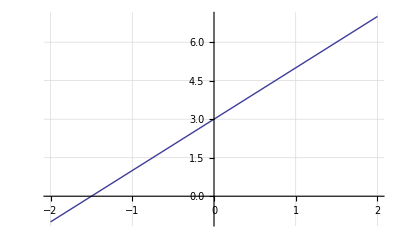

```mathematica
Plot[y = 2x+3, {x, -2, 2}, Axes->True, GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed]]
(* Plot it to solve. Intersect at (0,3) *)
```

```mathematica
Manipulate[Plot[{Exp[x*a], Exp[(x*a) + 0.25], Exp[(x*a) + 0.5], Exp[(x*a) + 0.75]},
{x, -20, 20}] , {a, 0.1, 0.5}](* always y-intersect at (0, 1) *)
```

```mathematica
Integrate[(1+x^2)^(-5/2), x]
```

(x (3+2 x^2))/(3 (1+x^2)^(3/2))

```mathematica
Manipulate[Plot[(x^a)+3, {x, -2, 2}, Filling -> Axis,
GridLines->Automatic, Ticks->Automatic, Mesh->False,
Frame->False, AxesLabel->{"x", "y = f(x)"},
LabelStyle->Directive[Blue,Bold],
GridLinesStyle->Directive[LightGray,Dashed]], {a, 2, 16, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[(((x*a)+2)*((x*a)-5))/(((x*a)-3)*((x*a)+1)), {x, -2, 2},
Filling -> Axis], {a, 1, 10}, SaveDefinitions->True]
```

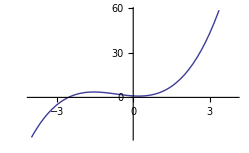

```mathematica
Plot[x^3+2 x^2-x+1,{x, -4, 4}, Filling -> None]
```

```mathematica
myRange = Range[2Pi];
```

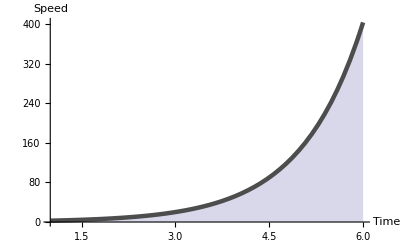

```mathematica
Plot[Exp[x],{x, Min[myRange], Max[myRange]}, Filling -> Axis,
AxesLabel->{"Time", "Speed"}, PlotStyle->{GrayLevel[.3], Thickness[0.008]},
PlotRangePadding->0.5]
```

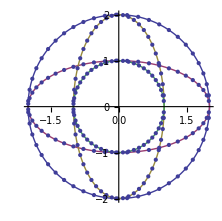

```mathematica
ParametricPlot[{{2Cos[t], 2Sin[t]}, {2Cos[t], Sin[t]},
{Cos[t], 2Sin[t]}, {Cos[t], Sin[t]}}, {t, 0, 2Pi}, Mesh->True]
```

```mathematica
Plot[1/x, {x, -4, 0.1, 4}, Filling -> None]
```

Plot::pllim: Range specification {x, -4, 0.1, 4} is not of the form {x, xmin, xmax}.

Plot[1/x,{x,-4,0.1,4},Filling→None]

```mathematica
theIntegral = ∫_1^100 f(x2+30)ⅆx (* Input d as [ESC]dd[ESC] *)
```

99 f (30+x2)

```mathematica
(* Get info about a variable with "?" *)
```

```mathematica
?theIntegral
```

Global`theIntegral

theIntegral=99 f (30+x2)

```mathematica
(* Get info about a data type with "Head" *)
```

```mathematica
Head[2]
```

Integer

```mathematica
Head[-45.21]
```

Real

```mathematica
Head[myIntegral]
```

Symbol

```mathematica
(* Some integrals... *)
```

```mathematica
∫_1^Pi Sin[x]ⅆx
```

1+Cos[1]

```mathematica
∫_0^(2Pi) Sin[x]ⅆx
```

0

```mathematica
Integrate[Sin[x], {x, 0, 2Pi}] (* Another way to write the same as example above *)
```

0

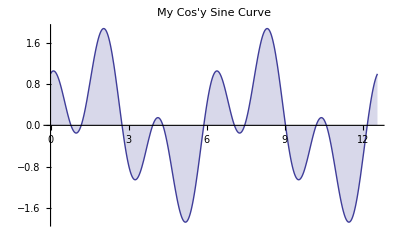

```mathematica
Plot[Sin[x]+Cos[3x], {x, 0, 4Pi}, Filling->Axis, GridLines->{Range[0, Pi*3, Pi], Range[-1, 1, 0.5]},
GridLinesStyle->LightGray,PlotLabel->"My Cos'y Sine Curve"]
```

```mathematica
myParetoListLabels = {"The first", "Another", "A third", "Four here", "High five"};
myParetoListData = Sort[{45, 123, 10, 167, 18}];
myParetoListDataBars = {0, 0, 0, 0, 0};
myParetoListDataDesc = Sort[myParetoListData, Greater];
myParetoListDataPercent = ConstantArray[0, Length[myParetoListDataDesc]];
myCounter = 1;
While[myCounter <= Length[myParetoListData],
myParetoListDataBars[[myCounter]] = myParetoListDataDesc[[myCounter]]/Total[myParetoListDataDesc]*100;
myParetoListDataPercent[[myCounter]] = (Total[Take[myParetoListDataDesc,{1, myCounter}]]*100)/ Total[myParetoListData];
myCounter++;
];
```

```mathematica
myBarChart = BarChart[myParetoListDataBars, ChartStyle->"DarkRainbow",
GridLines->{Range[0], Range[0, 100, 10]}, PlotLabel->"My Pareto Chart",
GridLinesStyle->LightGray, AxesLabel->{"Data", "Frequency"},
BarSpacing->{0,0},
PlotRange->{Automatic, {-5, 100}},(* NOTE: PlotRange from -5 to show bar labels *)
ChartElementFunction->"GlassRectangle", ChartLabels->myParetoListLabels];
```

```mathematica
myListLinePlot = ListLinePlot[myParetoListDataPercent,
PlotRange->Automatic,
Ticks->{None, Automatic}, Filling->None]; (* Dropped: DataRange->{Min[myParetoListData], Max[myParetoListData]}, *)
```

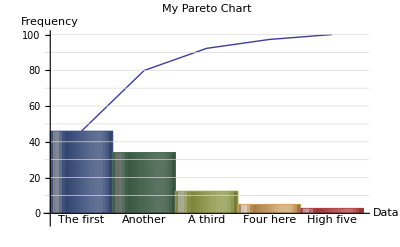

```mathematica
Show[myBarChart, myListLinePlot] (* TODO: Variant with Y-range to Total[data] *)
```

```mathematica
{N[myParetoListDataPercent], N[myParetoListDataBars]}
```

{{46.0055,79.8898,92.2865,97.2452,100.},{46.0055,33.8843,12.3967,4.95868,2.75482}}

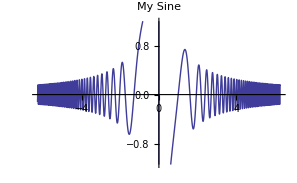

```mathematica
Plot[Sin[x^3-1]/x, {x, -2Pi, 2Pi}, GridLines->None,PlotLabel->"My Sine"]
```

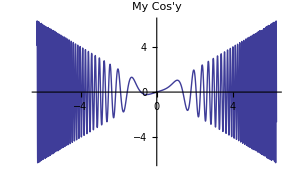

```mathematica
Plot[Cos[-x^3+1]*x, {x, -2Pi, 2Pi}, GridLines->None,PlotLabel->"My Cos'y"]
```

```mathematica
GetCurve[x_, y_]:=Module[{},
x^5 + (x * y) + y^5
];
Plot3D[GetCurve[x, y],{x,-Pi,Pi},{y,-Pi,Pi},Mesh->Automatic,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
GetCurveAgain[x_, y_]:=x^4 + (x * y) + y^-3;
x = Range[1, 10]; y = Range[1, 20, 2];
GetCurveAgain[x, y]
Plot3D[GetCurveAgain[x, y],{x,-Pi*10,Pi*10},{y,-Pi,Pi},Mesh->Automatic,MeshFunctions->Automatic]
```

{3,595/27,12001/125,97413/343,488431/729,1812823/1331,5474925/2197,14229001/3375,32985883/4913,69893211/6859}

-Graphics3D-